# Assignment 3 - Part 1 (Problem 1 & 2)

## Thu Si Nguyen Mai - s4278836

## A3-1

```mathematica
Quit[]
```

```mathematica
mA={{-1/8, -3/8, 3/8},{-1/8, -3/8, 1/8},{1/4, -1/4, 0}};
MatrixForm[mA]
mB={{-7/8, 5/8, -5/8}, {1/8, -3/8, -1/8}, {-1/2, 1/2, -1}};
MatrixForm[mB]
mC={{-1/3, 0, 2/3}, {-2/3, 1/3,0},{-2/3, 2/3, 1/3}};
MatrixForm[mC]
mD={{-5/6,1/2,1/2},{-1/2,1/6,-1/2},{-1,1,-1/3}};
MatrixForm[mD]
```

(-1/8 | -3/8 | 3/8
-1/8 | -3/8 | 1/8
1/4 | -1/4 | 0)

(-7/8 | 5/8 | -5/8
1/8 | -3/8 | -1/8
-1/2 | 1/2 | -1)

(-1/3 | 0 | 2/3
-2/3 | 1/3 | 0
-2/3 | 2/3 | 1/3)

(-5/6 | 1/2 | 1/2
-1/2 | 1/6 | -1/2
-1 | 1 | -1/3)

```mathematica
traces=Table[Tr[m],{m, {mA,mB,mC,mD}}];
Print["Traces of matrices A, B, C, D are, respectively, ", traces]

deter=Table[Det[m],{m, {mA,mB,mC,mD}}];
Print["Determinants of matrices A, B, C, D are, respectively, ",deter]

lambdas=Table[Eigenvalues[m],{m, {mA,mB,mC,mD}}];
names={"A", "B", "C", "D"};
Do[
Print["Eigenvalues of matrix ", names[[i]], ": ", lambdas[[i]]],
{i, 1, 4}
]

Print["For matrices A, B, C, D, trace equals sum of eigenvalues? ", Table[traces[[k]]==Total[lambdas[[k]]] ,{k,1,4}]]
Print["For matrices A, B, C, D, determinant equals product of eigenvalues? ",Table[deter[[k]]==Product[lambdas[[k,i]],{i, 1, Length[lambdas[[k]]]}], {k, 1, 4}]]
```

Traces of matrices A, B, C, D are, respectively, {-1/2,-9/4,1/3,-1}

Determinants of matrices A, B, C, D are, respectively, {1/32,-3/16,-5/27,-10/27}

Eigenvalues of matrix A: {-1/2,-1/4,1/4}

Eigenvalues of matrix B: {-3/2,-1/2,-1/4}

Eigenvalues of matrix C: {1/3+(2 ⅈ)/3,1/3-(2 ⅈ)/3,-1/3}

Eigenvalues of matrix D: {-1/3+ⅈ,-1/3-ⅈ,-1/3}

For matrices A, B, C, D, trace equals sum of eigenvalues? {True,True,True,True}

For matrices A, B, C, D, determinant equals product of eigenvalues? {True,True,True,True}

```mathematica
(*Assume that these matrices are Jacobian matrices at an equilibrium of a three-dimensional system of ODEs*)
stability={};
osci={};
Table[
re=Re[lambdas[[k]]];
im=Im[lambdas[[k]]];
If[re[[1]]<0 && re[[2]]<0&&re[[3]]<0,AppendTo[stability,"stable"],AppendTo[stability,"unstable"]]; (*stable if real parts of all eigenvalues are negative*)
If[im[[1]]!=0 || im[[2]]!=0 ||im[[3]]!=0, AppendTo[osci, "oscillatory/spiral"], AppendTo[osci,"monotonic/node"]], (*spiral if there are >=1 non-zero imaginary parts*)
{k, 1, 4}
];
stability
osci
```

{unstable,stable,unstable,stable}

{monotonic/node,monotonic/node,oscillatory/spiral,oscillatory/spiral}

```mathematica
(*Assume that these matrices are Jacobian matrices at an equilibrium of a three-dimensional system of recurrence equations*)
stability={};
osci={};
Table[
modul=Abs[lambdas[[k]]];
re=Re[lambdas[[k]]];
im=Im[lambdas[[k]]];
If[modul[[1]]<1 && modul[[2]]<1&&modul[[3]]<1,AppendTo[stability,"stable"],AppendTo[stability,"unstable"]]; (*stable if all eigenvalues have absolutes/moduli <1*)
If[im[[1]]!=0 || im[[2]]!=0 ||im[[3]]!=0||re[[1]]<0||re[[2]]<0||re[[3]]<0, AppendTo[osci, "oscillatory/spiral"], AppendTo[osci,"monotonic/node"]],(*spiral if there are >=1 non-zero imaginary parts OR >=1 negative REAL eigenvalues*)
{k, 1, 4}
];
stability
osci
```

{stable,unstable,stable,unstable}

{oscillatory/spiral,oscillatory/spiral,oscillatory/spiral,oscillatory/spiral}

## A3-2

```mathematica
Quit[]
```

```mathematica
param={r->5, f->2, b->1, d->5, phi->1, beta->1, delta->2};
res=r*N1*(1-(N1/k))-f*N1*N2/.param
herbi=N2*(b*N1-d)-phi*N2*N3/.param
carni=N3*(beta*N2-delta)/.param
```

5 N1 (1-N1/k)-2 N1 N2

(-5+N1) N2-N2 N3

(-2+N2) N3

```mathematica
eqVal=Values[Solve[{res==0,herbi==0,carni==0}, {N1, N2, N3}]]
```

{{0,2,-5},{k,0,0},{k/5,2,1/5 (-25+k)},{5,(5 (-5+k))/(2 k),0},{0,0,0}}

```mathematica
(*Four possibly meaningful equilibria*)
eqVal=Drop[eqVal,1]
```

{{k,0,0},{k/5,2,1/5 (-25+k)},{5,(5 (-5+k))/(2 k),0},{0,0,0}}

```mathematica
Print["Equilibrium 1 is biologically meaningful for ", Reduce[eqVal[[1]]>=0,k]]
Print["Equilibrium 2 is biologically meaningful for ", Reduce[eqVal[[2]]>=0,k]]
Print["Equilibrium 3 is biologically meaningful for ", Reduce[eqVal[[3]]>=0,k]]
```

Equilibrium 1 is biologically meaningful for k≥0

Equilibrium 2 is biologically meaningful for k≥25

Equilibrium 3 is biologically meaningful for k<0||k≥5

```mathematica
plotEqK={};
Do[
p=Plot[{eqVal[[i,1]],eqVal[[i,2]],eqVal[[i,3]]}, {k, 0.1, 40}, PlotStyle->{RGBColor["#2dac7d"], Orange, Brown}, 
PlotLabel->eqVal[[i]], PlotLegends->{"N1", "N2", "N3"},ImageSize->{350,300}, Frame->True, FrameLabel->{"K", "Population density"}];
AppendTo[plotEqK,p],
{i,1,3}
];
GraphicsRow[plotEqK, ImageSize->Full]
```

-Graphics-

```mathematica
(*only N1 exist*)
Reduce[eqVal[[3,2]]==0 ,k]
```

k==5

```mathematica
(*N1 and N2 coexist but N3 excluded*)
Reduce[eqVal[[2,1]]>0 && eqVal[[2,3]]==0,k]
Reduce[eqVal[[3,2]]>0,k]
```

k==25

k<0||k>5

```mathematica
(*all 3 species coexist*)
Reduce[eqVal[[2,1]]>0 && eqVal[[2,3]]>0,k]
```

k>25

```mathematica
j=D[{res, herbi, carni}, {{N1, N2, N3}}] ;(*Jacobian matrix*)
MatrixForm[j]
```

(-(5 N1)/k+5 (1-N1/k)-2 N2 | -2 N1 | 0
N2 | -5+N1-N3 | -N2
0 | N3 | -2+N2)

```mathematica
eiEqK=Table[Eigenvalues[j/.{N1->eqVal[[i,1]], N2->eqVal[[i,2]], N3->eqVal[[i,3]]}],{i, 1, Length[eqVal]}];
reEqK=Re[eiEqK]
imEqK=Im[eiEqK]
```

{{-5,-2,-5+Re[k]},{1/5 Re[Root[-1250+50 k+(-250+30 k) #1+5 #1^2+#1^3&,1]],1/5 Re[Root[-1250+50 k+(-250+30 k) #1+5 #1^2+#1^3&,2]],1/5 Re[Root[-1250+50 k+(-250+30 k) #1+5 #1^2+#1^3&,3]]},{1/2 Re[(-25+k)/k],5/2 Re[(-5 k^2-√(25 k^4+20 k^5-4 k^6))/k^3],5/2 Re[(-5 k^2+√(25 k^4+20 k^5-4 k^6))/k^3]},{-5,5,-2}}

{{0,0,Im[k]},{1/5 Im[Root[-1250+50 k+(-250+30 k) #1+5 #1^2+#1^3&,1]],1/5 Im[Root[-1250+50 k+(-250+30 k) #1+5 #1^2+#1^3&,2]],1/5 Im[Root[-1250+50 k+(-250+30 k) #1+5 #1^2+#1^3&,3]]},{1/2 Im[(-25+k)/k],5/2 Im[(-5 k^2-√(25 k^4+20 k^5-4 k^6))/k^3],5/2 Im[(-5 k^2+√(25 k^4+20 k^5-4 k^6))/k^3]},{0,0,0}}

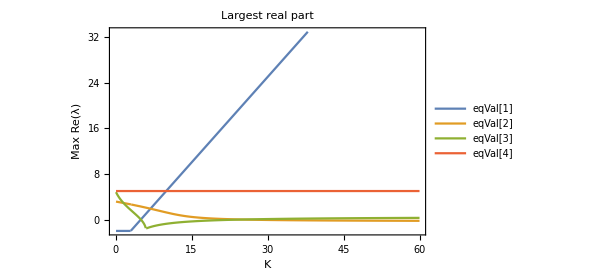

```mathematica
maxRe=Table[Max[reEqK[[i]]], {i, 1, Length[eqVal]}];
plotMaxRe= Plot[maxRe, {k, 0.1, 60},AxesOrigin->{0,0}, PlotLegends->{"eqVal[1]", "eqVal[2]", "eqVal[3]", "eqVal[4]"}, PlotLabel->"Largest real part",Frame->True,FrameLabel->{"K", "Max Re(λ)"},
ImageSize->{450,300}]
```

-Graphics-

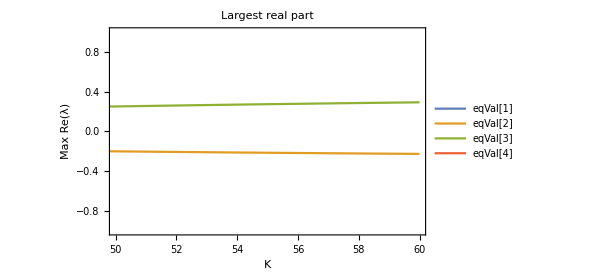

```mathematica
zoom1=Show[plotMaxRe, 
PlotRange->{{4.5,5.5},{-1,1}}];
zoom2=Show[plotMaxRe,
PlotRange->{{24.5, 25.5}, {-0.1, 0.1}}];
GraphicsRow[{zoom1, zoom2}, ImageSize->Full]
Show[plotMaxRe, PlotRange->{{50, 60}, {-1, 1}}]
```

```mathematica
(*Check the eigenvalues for K=5 and K=25*)
N[eiEqK/.k->5]
N[eiEqK/.k->25]
```

{{-5.,-2.,0.},{2.28428,-1.64214-0.897542 ⅈ,-1.64214+0.897542 ⅈ},{-2.,-5.,0.},{-5.,5.,-2.}}

{{-5.,-2.,20.},{0.,-0.5-4.4441 ⅈ,-0.5+4.4441 ⅈ},{0.,-0.5-4.4441 ⅈ,-0.5+4.4441 ⅈ},{-5.,5.,-2.}}

```mathematica
spiralOrNot={};
Do[
sp={};
Do[
im=Im[eiEqK[[i]]/.k->j];
If[im[[1]]!=0 ||im[[2]]!=0||im[[3]]!=0,AppendTo[sp, {j,1}], AppendTo[sp,{j,0}]], (*Oscillations if one of the imaginary parts !=0*)
{j, 0.1, 60,0.1}
]; 
AppendTo[spiralOrNot, sp],
{i, 1, 4}
];
```

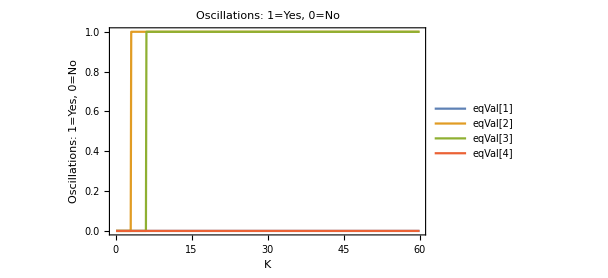

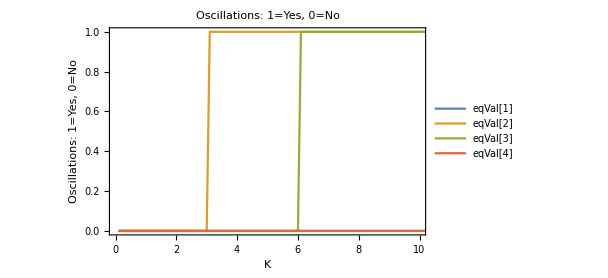

```mathematica
plotSON=ListLinePlot[spiralOrNot, PlotLegends->{"eqVal[1]", "eqVal[2]", "eqVal[3]", "eqVal[4]"}, PlotLabel->"Oscillations: 1=Yes, 0=No",Frame->True,FrameLabel->{"K", "Oscillations: 1=Yes, 0=No"},
ImageSize->{450,300} ]
Show[plotSON, PlotRange->{{0, 10}, All}]
```

```mathematica
(*Check imaginary parts of all eigenvalues of eqVal[3] at K=6 and at K=6.1*)
Im[eiEqK[[3]]/.k->6.0]
Im[eiEqK[[3]]/.k->6.1]
```

{0,0,0}

{0,-0.555929,0.555929}

```mathematica
plotTimePhase[k_,n10_,n20_,n30_,tmin_,tmax_]:=Module[{r=5, f=2, b=1, d=5, phi=1, beta=1, delta=2, eq1, eq2, eq3, init, sol1, sol2, sol3,tp, pp},
eq1=D[N1[t],t]==r*N1[t]*(1-(N1[t]/k))-f*N1[t]*N2[t];
eq2=D[N2[t],t]==N2[t]*(b*N1[t]-d)-phi*N2[t]*N3[t];
eq3=D[N3[t],t]==N3[t]*(beta*N2[t]-delta);
init={N1[0]==n10, N2[0]==n20, N3[0]==n30};
{sol1, sol2, sol3}=NDSolveValue[{eq1, eq2, eq3, init}, {N1[t], N2[t], N3[t]},{t, tmin, tmax}];
tp=Plot[{sol1, sol2, sol3}, {t, tmin, tmax}, PlotStyle->{RGBColor["#2dac7d"], Orange, Brown}, 
PlotLabel->"Time plot", PlotLegends->{"N1", "N2", "N3"},ImageSize->{450,300}, Frame->True, FrameLabel->{"t", "Population density"}];
pp=ParametricPlot3D[{sol1, sol2, sol3}, {t, tmin, tmax}, 
PlotLabel->"Phase plot", AxesLabel->{"N1", "N2", "N3"},BoxRatios->{1, 1, 1}, PlotRange->Full,ImageSize->Medium];
Row[{Show[tp], Show[pp]}]
]
```

```mathematica
Manipulate[plotTimePhase[k, n10, n20, n30, tmin, tmax], {{k, 20}, 0.01, 50, 0.1}, {n10, 10}, {n20, 10}, {n30, 10}, {tmin, 0}, {tmax, 40}]
```